## Run Me

```mathematica
Quit[]
```

```mathematica
AppendTo[$Path, "/Users/martines/Desktop/HighPT"];
```

```mathematica
<<HighPT`
```

-Graphics-

Authors: Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo, Olcyr Sumensari, and Felix Wilsch

References: arXiv:2207.10756http://arxiv.org/abs/2207.10756Nonehttp://arxiv.org/abs/2207.10756HyperlinkHyperlinkActive, arXiv:2207.10714http://arxiv.org/abs/2207.10714Nonehttp://arxiv.org/abs/2207.10714HyperlinkHyperlinkActive

Website: https://highpt.github.iohttps://highpt.github.ioNonehttps://highpt.github.ioHyperlinkHyperlinkActive

HighPT is free software released under the terms of the MIT License.

Version: 1.0.2

____________________________________

Initialized SMEFT mode:

Maximum operator dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

```mathematica
PartonicCrossSectionVH[s, {d[1], d[1]}]//FullSimplify//TraditionalForm
```

1/(1152 π s^2 𝓋^2 M_Z^2)√((-2 M_h^2 (M_Z^2+s)+M_h^4+(s-M_Z^2)^2)/s^2) (2 M_Z^2 ((-2 M_h^2 (M_Z^2+s)+M_h^4+4 s M_Z^2+M_Z^4+s^2) Abs[[f_(V, 2{regular,{0,0}})^L]_(d[1]d[1])]^2+(-2 M_h^2 (M_Z^2+s)+M_h^4+4 s M_Z^2+M_Z^4+s^2) Abs[[f_(V, 2{regular,{0,0}})^R]_(d[1]d[1])]^2+3 s (-M_h^2+M_Z^2+s) ([f_(V, 1{regular,{0,0}})^L]_(d[1]d[1]) Conjugate[([f_(V, 2{regular,{0,0}})^L]_(d[1]d[1]))]+[f_(V, 2{regular,{0,0}})^L]_(d[1]d[1]) Conjugate[([f_(V, 1{regular,{0,0}})^L]_(d[1]d[1]))]+[f_(V, 1{regular,{0,0}})^R]_(d[1]d[1]) Conjugate[([f_(V, 2{regular,{0,0}})^R]_(d[1]d[1]))]+[f_(V, 2{regular,{0,0}})^R]_(d[1]d[1]) Conjugate[([f_(V, 1{regular,{0,0}})^R]_(d[1]d[1]))]))+s (-2 M_h^2 (M_Z^2+s)+M_h^4+10 s M_Z^2+M_Z^4+s^2) Abs[[f_(V, 1{regular,{0,0}})^L]_(d[1]d[1])]^2+s (-2 M_h^2 (M_Z^2+s)+M_h^4+10 s M_Z^2+M_Z^4+s^2) Abs[[f_(V, 1{regular,{0,0}})^R]_(d[1]d[1])]^2)

```mathematica
λ[s_] := (1 - 2 (Mass["ZBoson"]^2+ Mass["Higgs"]^2)/s + ((Mass["ZBoson"]^2- Mass["Higgs"]^2)^2)/s^2)/.GetParameters[]
```

```mathematica
λ[0.01(Mass["ZBoson"]^2+ Mass["Higgs"]^2)^2/.GetParameters[]]
```

0.991665

```mathematica
Mass["ZBoson"]/.GetParameters[]
```

91.1876

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
pT[y_] :=( 1/(4 Cosh[y]^2)(((s + Mass["Higgs"]^2-Mass["ZBoson"]^2)^2)/s- 4 Mass["Higgs"]^2 Cosh[y]^2))/.{s-> 1000
}/.GetParameters[]
```

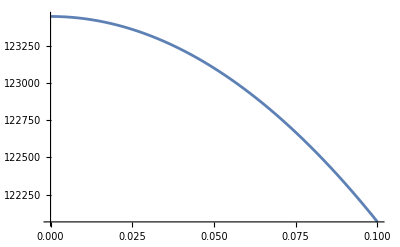

```mathematica
Plot[pT[x],{x, 0, 0.1}]
```

```mathematica
pT[1]
```

-9091.93

```mathematica
GeVtoTeV = 0.001;
```

```mathematica
mH = 125 * GeVtoTeV
```

0.125

```mathematica
mZ = 91 * GeVtoTeV
```

0.091

```mathematica
pT[y_]:= (((s + mH^2-mZ^2)^2)/(4s Cosh[y]^2)- mH^2 )/.s->(mH^2+mZ^2)^2
```

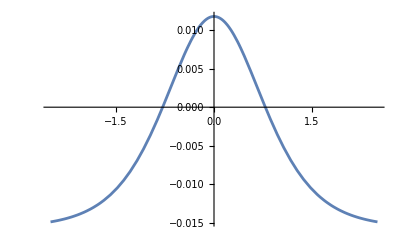

```mathematica
Plot[pT[y], {y, -2.5, 2.5}]
```

```mathematica
WC["Hq3",{1,1}]//TraditionalForm
```

[𝒞_Hq^(3)]_11